```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dan/ResearchLocal/adiabatic/"];
```

```mathematica
fontweight="Bold"; fontsize=12;
```

## Strong Scaling (constant total domain size)

```mathematica
intelSS={
(*runID,cores,zones,cycles,walltime*)
{20,2^3,256^3,49,600},
{21,4^3,256^3,332,600},
{22,8^3,256^3,435,164.8}};
```

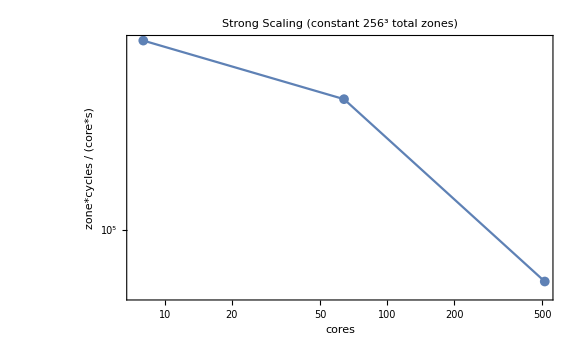

```mathematica
ListLogLogPlot[Transpose[{
intelSS[[All,2]],
intelSS[[All,3]]*intelSS[[All,4]]/(intelSS[[All,2]]*intelSS[[All,5]])
}]
,PlotLabel->"Strong Scaling (constant 256^3 total zones)",FrameLabel->{"cores","zone*cycles / (core*s)"},Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},Joined->True,ImageSize->Large]
```

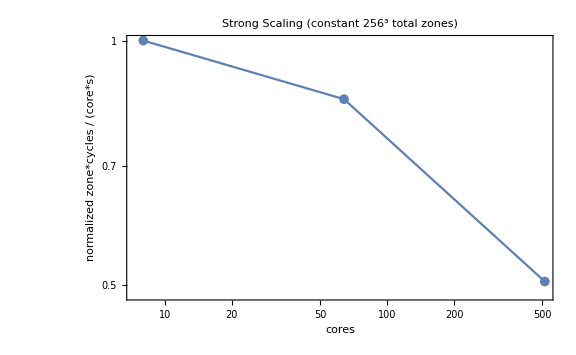

```mathematica
ssPlot=ListLogLogPlot[Transpose[{
intelSS[[All,2]],
intelSS[[All,3]]*intelSS[[All,4]]/(intelSS[[All,2]]*intelSS[[All,5]])/(intelSS[[1,3]]*intelSS[[1,4]]/(intelSS[[1,2]]*intelSS[[1,5]]))
}]
,PlotLabel->"Strong Scaling (constant 256^3 total zones)",FrameLabel->{"cores","normalized zone*cycles / (core*s)"},Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},Joined->True,ImageSize->Large]
```

```mathematica
Export["ssPlot.png",ssPlot]
```

ssPlot.png

## Weak Scaling (constant grids per core)

```mathematica
{148970,127270,99340}/148970//N
```

{1.,0.854333,0.666846}

```mathematica
6*32
```

192

```mathematica
intelWS={
(*runID,cores,zones,cycles,walltime*)
{38,2^3,(32*2)^3,2641,600},
{39,4^3,(32*4)^3,2329,600},
{40,8^3,(32*8)^3,1814,600},
{33,1*1*1,1*(32)^3,2739,600},
{34,2*1*1,2*(32)^3,2711,600},
{35,4*2*2,16*(32)^3,2549,600},
{36,4*3*2,24*(32)^3,2389,600},
{37,6*4*2,48*(32)^3,2319,600},
{41,5*2*2,20*(32)^3,2536,600},
{42,6*2*2,24*(32)^3,2395,600},
{43,4*4*2,32*(32)^3,2429,600},
{44,5*4*2,32*(32)^3,2489,600},
{44,5*4*2,32*(32)^3,2472,600},
{33,1*1*1,1*(32)^3,3017,600},
{34,2*1*1,2*(32)^3,2877,600},
{35,4*2*2,16*(32)^3,2581,600},
{36,4*3*2,24*(32)^3,2421,600},
{37,6*4*2,48*(32)^3,2429,600},
{38,2^3,(32*2)^3,2740,600},
{39,4^3,(32*4)^3,2413,600},
{40,8^3,(32*8)^3,1988,600},
{41,5*2*2,20*(32)^3,2525,600},
{42,6*2*2,24*(32)^3,2407,600},
{43,4*4*2,32*(32)^3,2364,600},
{44,5*4*2,32*(32)^3,2433,600},
{33,1*1*1,1*(32)^3,3017,600},
{34,2*1*1,2*(32)^3,2877,600},
{35,4*2*2,16*(32)^3,2581,600},
{36,4*3*2,24*(32)^3,2421,600},
{37,6*4*2,48*(32)^3,2429,600},
{38,2^3,(32*2)^3,2740,600},
{39,4^3,(32*4)^3,2413,600},
{40,8^3,(32*8)^3,1988,600},
{41,5*2*2,20*(32)^3,2525,600},
{42,6*2*2,24*(32)^3,2407,600},
{43,4*4*2,32*(32)^3,2364,600},
{44,5*4*2,32*(32)^3,2433,600}
};
```

```mathematica
5*4*2
```

40

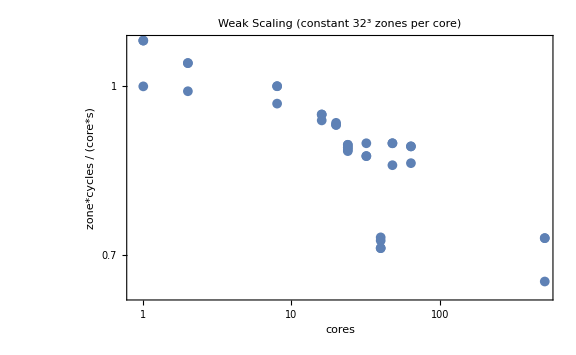

```mathematica
wsPlot=ListLogLogPlot[Transpose[{
intelWS[[All,2]],
intelWS[[All,3]]*intelWS[[All,4]]/(intelWS[[All,2]]*intelWS[[All,5]])/(intelWS[[4,3]]*intelWS[[4,4]]/(intelWS[[4,2]]*intelWS[[4,5]]))
}]
,PlotLabel->"Weak Scaling (constant 32^3 zones per core)",FrameLabel->{"cores","zone*cycles / (core*s)"},GridLines->{{24,48},{}},Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},ImageSize->Large]
```

## Consistency test (many short, 1 node jobs)

```mathematica
intelC={
(* runID, wallTime *)
{50,412.13},
{51,399.45},
{52,405.12},
{53,410.89},
{54,405.92},
{55,403.47},
{56,407.14},
{57,401.5} ,
{58,412.62},
{59,403.32}
};
```

```mathematica
mean=Mean[intelC[[All,2]]]//N
stdev=√Variance[intelC[[All,2]]]//N
stdev/mean
```

406.156

4.52016

0.0111291